## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
dirMathematica="C:\\Users\\danto\\Dropbox\\_mm\\";
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/db/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

Get::noopen: Cannot open utility modules.m.

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

printmem

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## data

### MoM data

```mathematica
data=Import[dirData<>"mom.txt","Data"];
Dimensions[%]
```

{361,10}

### slice

```mathematica
θ=data[[All,2]];
rcs=data[[All,5]];
```

```mathematica
Max[rcs]
Min[rcs]
```

-1.825

-46.72

```mathematica
plot=rcs+50;
```

```mathematica
ListPolarPlot[rcs,Joined->True];
```

```mathematica
alpha=ListPolarPlot[plot,Joined->True];
```

```mathematica
rings=Table[
ListPolarPlot[Table[10k,{360}],Joined->True,PlotStyle->Red]
,{k,5}];
```

```mathematica
g=Show[{rings,alpha}];
```

```mathematica
garrow=Graphics[{Thickness[0.01],Arrow[{o,{50,0}}]}];
```

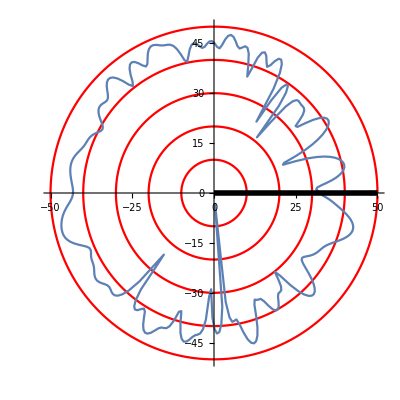

```mathematica
g=Show[{rings,alpha,garrow}]
```

```mathematica
tresExport["my-first-rcs",g]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```